# BDF Font translation

### Initialization

```mathematica
Off[General::spell,General::spell1]
```

### Function to expand hex numbers into bits

```mathematica
HexExpand=Function[{hex},Sign[BitAnd[ToExpression["16^^"<>hex],#]]&/@Table[2^b,{b,4 StringLength[hex]-1,0,-1}]]
```

Function[{hex},(Sign[BitAnd[ToExpression[16^^<>hex],#1]]&)/@Table[2^b,{b,4 StringLength[hex]-1,0,-1}]]

### Function to compress bit array into words

```mathematica
WordBuild=Function[{bitarray},Fold[2#1+#2&,0,bitarray]]
```

Function[{bitarray},Fold[2 #1+#2&,0,bitarray]]

## Import and process

```mathematica
SetDirectory["../src"]
```

/home/cmaier/Hackerspaces/sinobit/zpix-pixel-font/src

```mathematica
FileNames[]
```

{TGSCC-Unicode.txt,Zpix.bdf,Zpix.vfb}

```mathematica
Dimensions[bdflines=StringSplit/@Import["Zpix.bdf","Lines"]]
```

{393838}

```mathematica
Dimensions[rawunicodetable=Import["TGSCC-Unicode.txt","Table"]]
```

{8107}

```mathematica
Take[bdflines,200]
```

{{STARTFONT,2.1},{FONT,-FontForge-Zpix-Normal-R-Normal--12-120-75-75-P-119-ISO10646-1},{SIZE,12,75,75},{FONTBOUNDINGBOX,19,13,-5,-2},{COMMENT,"Generated,by,fontforge,,http://fontforge.sourceforge.net"},{STARTPROPERTIES,39},{FOUNDRY,"FontForge"},{FAMILY_NAME,"Zpix"},{WEIGHT_NAME,"Normal"},{SLANT,"R"},{SETWIDTH_NAME,"Normal"},{ADD_STYLE_NAME,""},{PIXEL_SIZE,12},{POINT_SIZE,120},{RESOLUTION_X,75},{RESOLUTION_Y,75},{SPACING,"P"},{AVERAGE_WIDTH,119},{CHARSET_REGISTRY,"ISO10646"},{CHARSET_ENCODING,"1"},{FONTNAME_REGISTRY,""},{CHARSET_COLLECTIONS,"ASCII,ISOLatin1Encoding,ISO8859-5,JISX0208.1997,GB2312.1980,BIG5,ISO10646-1"},{FONT_NAME,"Zpix"},{FACE_NAME,"ZpixEX2"},{FONT_VERSION,"2.0"},{FONT_ASCENT,10},{FONT_DESCENT,2},{UNDERLINE_POSITION,-1},{UNDERLINE_THICKNESS,1},{X_HEIGHT,6},{CAP_HEIGHT,8},{RAW_ASCENT,796},{RAW_DESCENT,203},{NORM_SPACE,5},{RELATIVE_WEIGHT,40},{RELATIVE_SETWIDTH,50},{SUPERSCRIPT_X,0},{SUPERSCRIPT_Y,6},{SUPERSCRIPT_SIZE,6},{SUBSCRIPT_X,0},{SUBSCRIPT_Y,0},{SUBSCRIPT_SIZE,6},{FIGURE_WIDTH,6},{AVG_LOWERCASE_WIDTH,89},{AVG_UPPERCASE_WIDTH,95},{ENDPROPERTIES},{CHARS,22043},{STARTCHAR,space},{ENCODING,32},{SWIDTH,333,0},{DWIDTH,4,0},{BBX,1,1,13,-2},{BITMAP},{00},{ENDCHAR},{STARTCHAR,exclam},{ENCODING,33},{SWIDTH,300,0},{DWIDTH,6,0},{BBX,1,9,2,0},{BITMAP},{80},{80},{80},{80},{80},{80},{00},{80},{80},{ENDCHAR},{STARTCHAR,quotedbl},{ENCODING,34},{SWIDTH,378,0},{DWIDTH,6,0},{BBX,3,2,1,7},{BITMAP},{A0},{A0},{ENDCHAR},{STARTCHAR,numbersign},{ENCODING,35},{SWIDTH,601,0},{DWIDTH,6,0},{BBX,5,9,0,0},{BITMAP},{50},{50},{F8},{50},{50},{50},{F8},{50},{50},{ENDCHAR},{STARTCHAR,dollar},{ENCODING,36},{SWIDTH,628,0},{DWIDTH,6,0},{BBX,5,11,0,-1},{BITMAP},{20},{70},{A8},{A0},{60},{20},{30},{28},{A8},{70},{20},{ENDCHAR},{STARTCHAR,percent},{ENCODING,37},{SWIDTH,968,0},{DWIDTH,6,0},{BBX,6,8,0,0},{BITMAP},{48},{A8},{B0},{50},{28},{34},{54},{48},{ENDCHAR},{STARTCHAR,ampersand},{ENCODING,38},{SWIDTH,769,0},{DWIDTH,6,0},{BBX,5,9,0,0},{BITMAP},{60},{90},{90},{60},{40},{A8},{A8},{90},{68},{ENDCHAR},{STARTCHAR,quotesingle},{ENCODING,39},{SWIDTH,203,0},{DWIDTH,6,0},{BBX,1,2,2,7},{BITMAP},{80},{80},{ENDCHAR},{STARTCHAR,parenleft},{ENCODING,40},{SWIDTH,359,0},{DWIDTH,6,0},{BBX,3,11,2,-1},{BITMAP},{20},{40},{40},{80},{80},{80},{80},{80},{40},{40},{20},{ENDCHAR},{STARTCHAR,parenright},{ENCODING,41},{SWIDTH,359,0},{DWIDTH,6,0},{BBX,3,11,1,-1},{BITMAP},{80},{40},{40},{20},{20},{20},{20},{20},{40},{40},{80},{ENDCHAR},{STARTCHAR,asterisk},{ENCODING,42},{SWIDTH,437,0},{DWIDTH,6,0},{BBX,5,5,0,2},{BITMAP},{20},{20},{F8},{20}}

```mathematica
Take[rawunicodetable,32]
```

{{#,Table,of,General,Standard,Chinese,Characters,mapped,to,Unicode},{index,number,codepoint},{1,U+4E00},{2,U+4E59},{3,U+4E8C},{4,U+5341},{5,U+4E01},{6,U+5382},{7,U+4E03},{8,U+535C},{9,U+516B},{10,U+4EBA},{11,U+5165},{12,U+513F},{13,U+5315},{14,U+51E0},{15,U+4E5D},{16,U+5201},{17,U+4E86},{18,U+5200},{19,U+529B},{20,U+4E43},{21,U+53C8},{22,U+4E09},{23,U+5E72},{24,U+4E8E},{25,U+4E8F},{26,U+5DE5},{27,U+571F},{28,U+58EB},{29,U+624D},{30,U+4E0B}}

### Split font file in character descriptions

```mathematica
Transpose[Flatten[Position[bdflines,#]]&/@{{"STARTCHAR",_},{"ENDCHAR"}}];
Dimensions[charlines=Take[bdflines,#]&/@%]
```

{22043}

```mathematica
charlines⟦1⟧
```

{{STARTCHAR,space},{ENCODING,32},{SWIDTH,333,0},{DWIDTH,4,0},{BBX,1,1,13,-2},{BITMAP},{00},{ENDCHAR}}

```mathematica
charlines⟦2⟧
```

{{STARTCHAR,exclam},{ENCODING,33},{SWIDTH,300,0},{DWIDTH,6,0},{BBX,1,9,2,0},{BITMAP},{80},{80},{80},{80},{80},{80},{00},{80},{80},{ENDCHAR}}

### Extract character codes

```mathematica
Dimensions[charcodes=Last[Flatten[Select[#,First[#]=="ENCODING"&]]]&/@charlines]
```

{22043}

### Extract character widths

```mathematica
Dimensions[widths=Flatten[Select[#,First[#]=="DWIDTH"&]]⟦2⟧&/@charlines]
```

{22043}

#### Character width statistics

```mathematica
TableForm[Sort[Tally[ToExpression/@widths],#1⟦1⟧<#2⟦1⟧&]]
```

0 | 2
2 | 6
3 | 2
4 | 1
6 | 305
8 | 2
9 | 3
10 | 3
11 | 3
12 | 21706
13 | 10

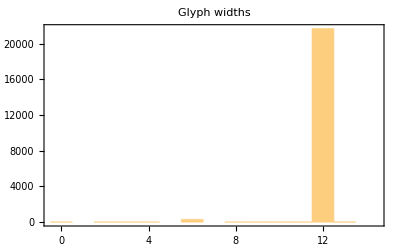

```mathematica
Print[Histogram[ToExpression/@widths,{-1/2,29/2,1},Frame->True,PlotRange->All,PlotLabel->"Glyph widths"]];
```

#### Indices of characters with widths ≠12

```mathematica
nonstdwidth=Flatten[Position[ToExpression/@widths,w_/;w≠12]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,100,101,104,105,106,107,108,109,110,113,114,115,117,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,325,326,329,332,333,336,339,345,346,347,349,350,351,352,353,354,355,356,357,358,359,360,361,362,364,365,366,369,370,372,373,374,375,376,387,388,403,404,405,407,412,416,418,419,420,437,441,442,451,452,667,668,1354,21834,21835,21836,21837,21838,21839,21840,21841,21842,21843,21855,21856,21857,21858,21859,21860,21861,21891,21974,21975,21976,21977,21978,21979,21980,21981,21982,21983,21984,21985,21986,21987,21988,21989,21990,21991,21992,21993,21994,21995,21996,21997,21998,21999,22000,22001,22002,22003,22004,22005,22006,22007,22008,22009,22010,22011,22012,22013,22014,22015,22016,22017,22018,22019,22020,22021,22022,22023,22024,22025,22026,22027,22028,22029,22030,22031,22032,22033,22034,22035,22036}

### Extract bounding box dimensions

```mathematica
Dimensions[boundingboxes=Flatten[Select[#,First[#]=="BBX"&]]&/@charlines]
```

{22043,5}

### Extract bounding box sizes

```mathematica
Dimensions[sizes=Take[#,{2,3}]&/@ToExpression[boundingboxes]]
```

{22043,2}

#### Maximum bounding box size

```mathematica
maxsize=MapThread[Apply,{{Max,Max},Transpose[sizes]}]
```

{12,12}

#### Bounding box size statistics

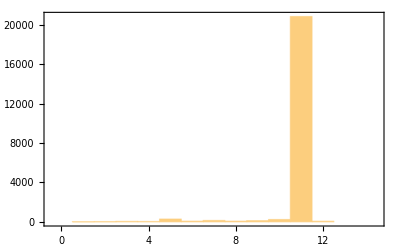

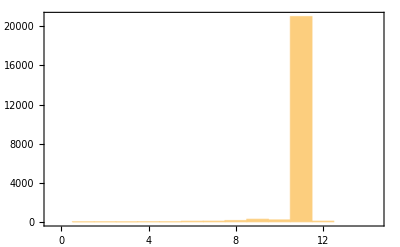

```mathematica
Print[Histogram[#,{-1/2,29/2,1},Frame->True,PlotRange->All]]&/@Transpose[sizes];
```

1
25 | 2
36 | 3
56 | 4
45 | 5
294 | 6
79 | 7
150 | 8
79 | 9
127 | 10
247 | 11
20832 | 12
73
1
27 | 2
28 | 3
23 | 4
35 | 5
31 | 6
76 | 7
84 | 8
147 | 9
281 | 10
212 | 11
21015 | 12
84

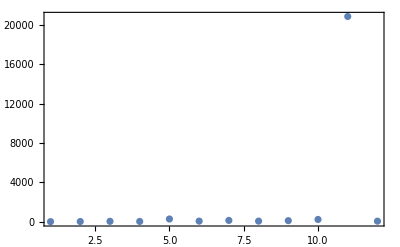

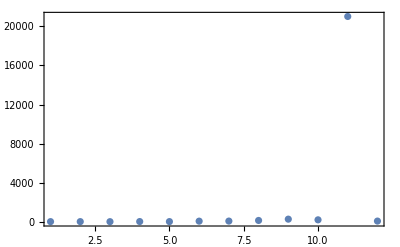

```mathematica
TableForm[Sort[Tally[#],#1⟦1⟧<#2⟦1⟧&]&/@Transpose[sizes]]
Print[ListPlot[#,Frame->True,PlotRange->All]]&/@%;
```

### Extract bounding box positions

```mathematica
bounds=Flatten[{Take[#,-2],Take[#,-2]+Take[#,{2,3}]}]&/@ToExpression[boundingboxes];
```

```mathematica
Dimensions[bounds]
```

{22043,4}

#### Envelope of all bounding boxes

```mathematica
bigbox=MapThread[Apply,{{Min,Min,Max,Max},Transpose[bounds]}]
```

{-5,-2,14,11}

#### Bounding box statistics

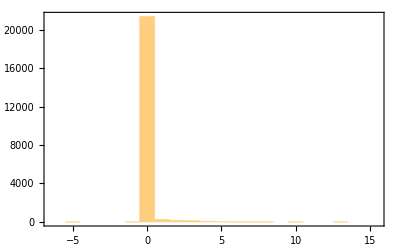

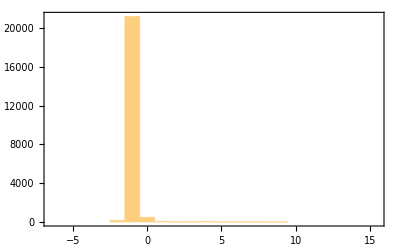

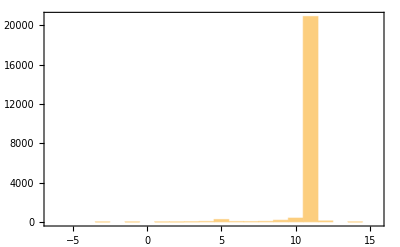

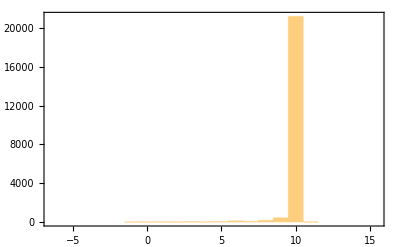

```mathematica
Print[Histogram[#,{-13/2,31/2,1},Frame->True,PlotRange->All]]&/@Transpose[bounds];
```

-5
2 | -1
1 | 0
21400 | 1
246 | 2
155 | 3
128 | 4
55 | 5
35 | 6
9 | 7
8 | 8
2 | 10
1 | 13
1 |  | 
-2
149 | -1
21225 | 0
475 | 1
54 | 2
20 | 3
26 | 4
47 | 5
6 | 6
15 | 7
13 | 8
10 | 9
3 |  |  | 
-3
1 | -1
1 | 1
3 | 2
4 | 3
24 | 4
50 | 5
247 | 6
43 | 7
38 | 8
56 | 9
174 | 10
395 | 11
20903 | 12
103 | 14
1
-1
3 | 0
3 | 1
7 | 2
4 | 3
13 | 4
5 | 5
41 | 6
102 | 7
56 | 8
155 | 9
419 | 10
21232 | 11
3 |  |

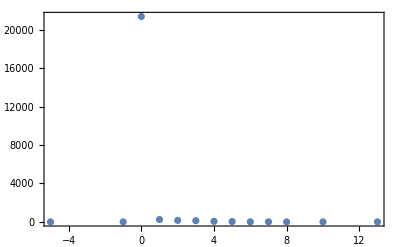

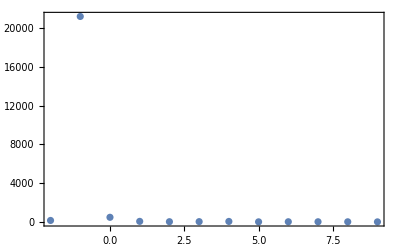

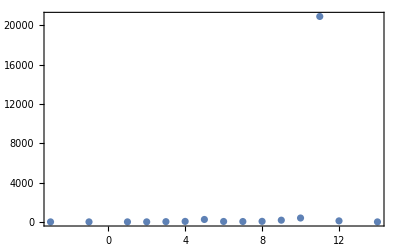

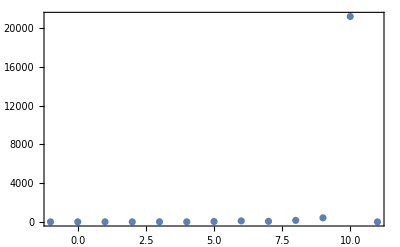

```mathematica
TableForm[Sort[Tally[#],#1⟦1⟧<#2⟦1⟧&]&/@Transpose[bounds]]
Print[ListPlot[#,Frame->True,PlotRange->All]]&/@%;
```

#### Indices of bounding box position outliers

```mathematica
outliers=Flatten[Position[bounds,{l_,b_,r_,t_}/;l<0||b<-1||r>11||t>11]]
```

{1,13,64,93,101,116,134,166,236,237,240,241,247,250,254,255,256,263,265,281,284,295,307,310,311,313,316,327,328,329,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,646,658,659,661,668,675,1033,2300,3362,5390,6077,6760,6787,8423,9419,13735,13789,14038,15261,15906,16400,17659,17900,20505,21427,21576,21590,21706,21829,21831,21840,21858,21877,21891,21942,21950,21953,21959,21960,21968,21971,22040}

### Extend glyph bitmaps to full font bounding box dimensions

```mathematica
fills=#-bigbox&/@bounds;
```

```mathematica
Take[fills,16]
```

{{18,0,0,-12},{7,2,-11,-2},{6,9,-10,-2},{5,2,-9,-2},{5,1,-9,-1},{5,2,-8,-3},{5,2,-9,-2},{7,9,-11,-2},{7,1,-9,-1},{6,1,-10,-1},{5,4,-9,-4},{5,4,-9,-4},{5,0,-12,-10},{5,6,-9,-6},{7,2,-11,-9},{6,2,-10,-2}}

```mathematica
Dimensions[bitmaps=Function[{line},
Block[{bounds=ToExpression[Drop[Flatten[Select[line,First[#]=="BBX"&]],1]]},
1-Take[HexExpand[#],bounds⟦1⟧]&/@Flatten[Take[line,{1,-1}+Flatten[Position[line,#]&/@{{"BITMAP"},{"ENDCHAR"}}]]]
]
]/@charlines]
```

{22043}

```mathematica
Take[bitmaps,16]
```

{{{1}},{{0},{0},{0},{0},{0},{0},{1},{0},{0}},{{0,1,0},{0,1,0}},{{1,0,1,0,1},{1,0,1,0,1},{0,0,0,0,0},{1,0,1,0,1},{1,0,1,0,1},{1,0,1,0,1},{0,0,0,0,0},{1,0,1,0,1},{1,0,1,0,1}},{{1,1,0,1,1},{1,0,0,0,1},{0,1,0,1,0},{0,1,0,1,1},{1,0,0,1,1},{1,1,0,1,1},{1,1,0,0,1},{1,1,0,1,0},{0,1,0,1,0},{1,0,0,0,1},{1,1,0,1,1}},{{1,0,1,1,0,1},{0,1,0,1,0,1},{0,1,0,0,1,1},{1,0,1,0,1,1},{1,1,0,1,0,1},{1,1,0,0,1,0},{1,0,1,0,1,0},{1,0,1,1,0,1}},{{1,0,0,1,1},{0,1,1,0,1},{0,1,1,0,1},{1,0,0,1,1},{1,0,1,1,1},{0,1,0,1,0},{0,1,0,1,0},{0,1,1,0,1},{1,0,0,1,0}},{{0},{0}},{{1,1,0},{1,0,1},{1,0,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{1,0,1},{1,0,1},{1,1,0}},{{0,1,1},{1,0,1},{1,0,1},{1,1,0},{1,1,0},{1,1,0},{1,1,0},{1,1,0},{1,0,1},{1,0,1},{0,1,1}},{{1,1,0,1,1},{1,1,0,1,1},{0,0,0,0,0},{1,1,0,1,1},{1,0,1,0,1}},{{1,1,0,1,1},{1,1,0,1,1},{0,0,0,0,0},{1,1,0,1,1},{1,1,0,1,1}},{{1,0},{1,0},{0,1}},{{0,0,0,0,0}},{{0},{0}},{{1,1,0},{1,1,0},{1,1,0},{1,0,1},{1,0,1},{1,0,1},{0,1,1},{0,1,1},{0,1,1}}}

```mathematica
BitmapExtend=Function[{bitmap,fill},
Block[{bmp,xl=Table[1,{☺,fill⟦1⟧}],xr=Table[1,{☺,-fill⟦3⟧}],yt,yb},
bmp=Join[xl,#,xr]&/@bitmap;
yb=Table[Table[1,{☺,Length[First[bmp]]}],{☹,fill⟦2⟧}];
yt=Table[Table[1,{☺,Length[First[bmp]]}],{☹,-fill⟦4⟧}];
Join[yt,bmp,yb]
]
]
```

Function[{bitmap,fill},Block[{bmp,xl=Table[1,{☺,fill⟦1⟧}],xr=Table[1,{☺,-fill⟦3⟧}],yt,yb},bmp=(Join[xl,#1,xr]&)/@bitmap;yb=Table[Table[1,{☺,Length[First[bmp]]}],{☹,fill⟦2⟧}];yt=Table[Table[1,{☺,Length[First[bmp]]}],{☹,-fill⟦4⟧}];Join[yt,bmp,yb]]]

```mathematica
Dimensions[extbitmaps=MapThread[BitmapExtend,{bitmaps,fills}]]
```

{22043,13,19}

```mathematica
bigbox
```

{-5,-2,14,11}

### Truncate glyphs to 12×12 bitmap

```mathematica
BitmapTruncate=Function[bitmap,Take[#,{6,17}]&/@Take[bitmap,{2,13}]]
```

Function[bitmap,(Take[#1,{6,17}]&)/@Take[bitmap,{2,13}]]

```mathematica
Dimensions[trbitmaps=BitmapTruncate/@extbitmaps]
```

{22043,12,12}

## Display glyphs

### Non standard width glyphs

```mathematica
nonstdwidthgraphics=MapThread[Graphics[Raster[Reverse[#1]],Frame->True,AspectRatio->Divide@@Dimensions[#1],FrameTicks->({#,#,{},{}}&[Range[0,16,4]]),PlotLabel->("code: 0x"<>IntegerString[ToExpression[#2],16,4]<>" width:"<>ToString[#3])]&,#⟦nonstdwidth⟧&/@{extbitmaps,charcodes,widths}];
```

```mathematica
nonstdwidthtruncgraphics=MapThread[Graphics[Raster[Reverse[#1]],Frame->True,AspectRatio->Divide@@Dimensions[#1],FrameTicks->({#,#,{},{}}&[Range[0,16,4]]),PlotLabel->("code: 0x"<>IntegerString[ToExpression[#2],16,4]<>" width:"<>ToString[#3])]&,#⟦nonstdwidth⟧&/@{trbitmaps,charcodes,widths}];
```

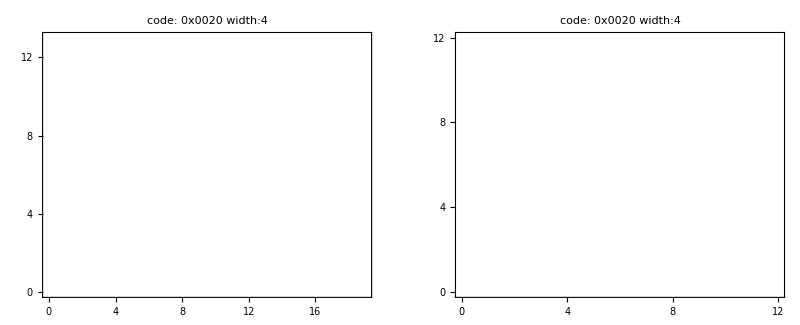

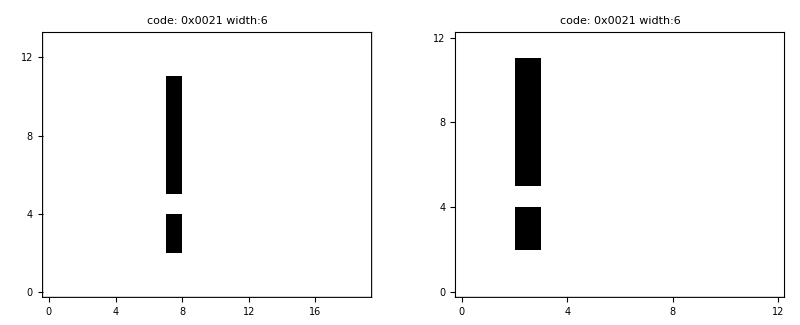

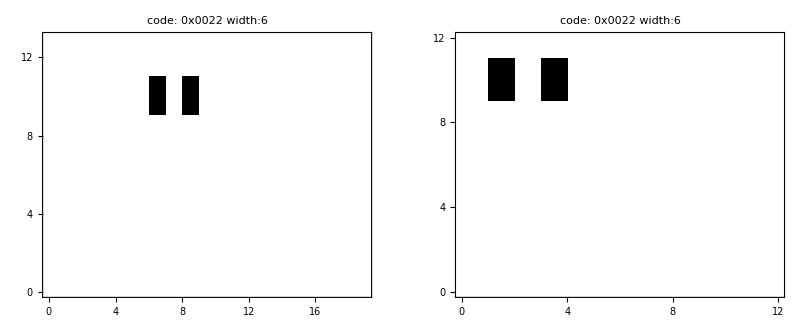

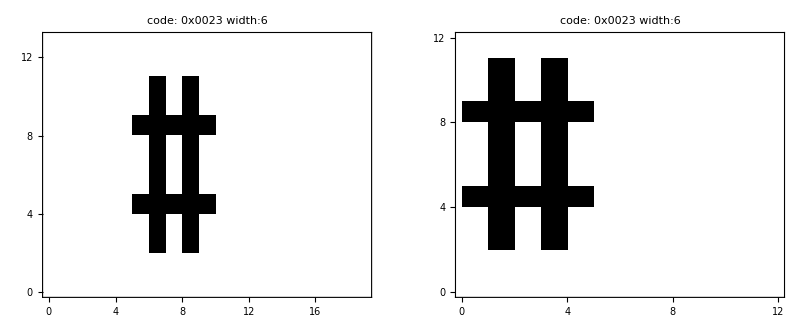

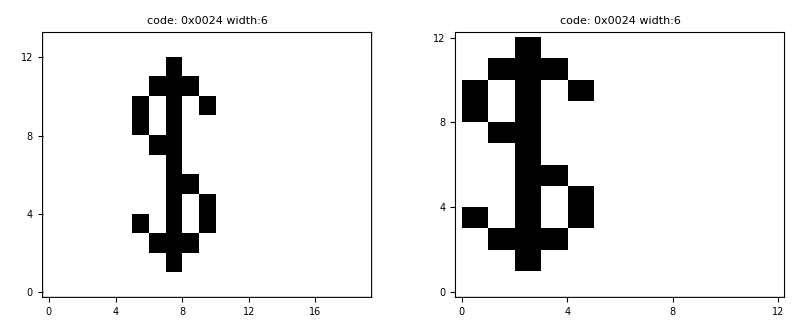

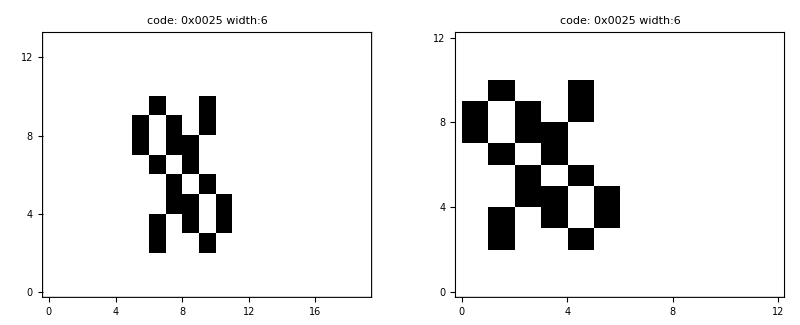

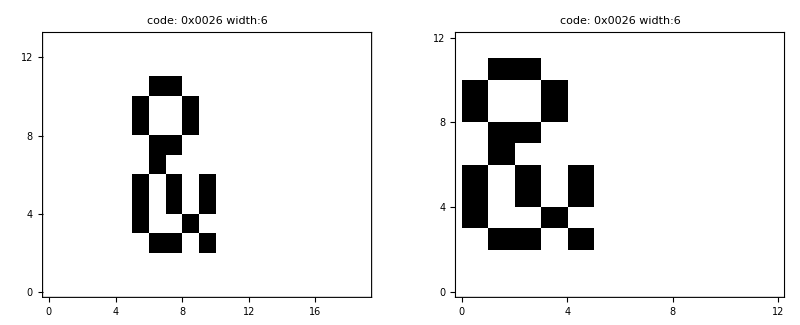

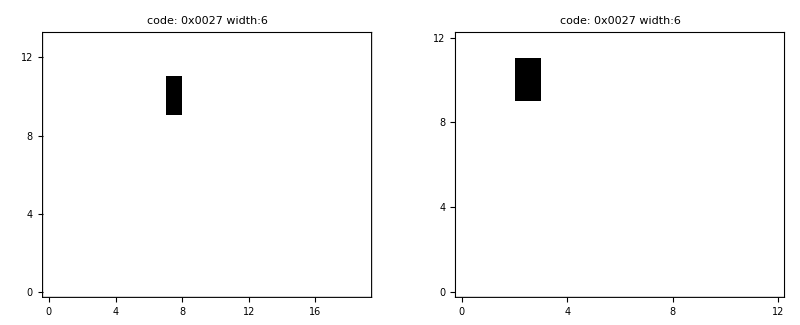

-Graphics-

-Graphics-

-Graphics-

«219 more identical outputs»

```mathematica
MapThread[Print[GraphicsGrid[{{##}}]]&,{nonstdwidthgraphics,nonstdwidthtruncgraphics}];
```

### Bounding box outlier glyphs

```mathematica
outliergraphics=MapThread[Graphics[Raster[Reverse[#1]],Frame->True,AspectRatio->Divide@@Dimensions[#1],FrameTicks->({#,#,{},{}}&[Range[0,16,4]]),PlotLabel->("code: 0x"<>IntegerString[ToExpression[#2],16,4]<>" width: "<>ToString[#3])]&,#⟦outliers⟧&/@{extbitmaps,charcodes,widths}];
```

```mathematica
outliertruncgraphics=MapThread[Graphics[Raster[Reverse[#1]],Frame->True,AspectRatio->Divide@@Dimensions[#1],FrameTicks->({#,#,{},{}}&[Range[0,16,4]]),PlotLabel->("code: 0x"<>IntegerString[ToExpression[#2],16,4])]&,#⟦outliers⟧&/@{trbitmaps,charcodes,widths}];
```

```mathematica
MapThread[Print[GraphicsGrid[{{##}}]]&,{outliergraphics,outliertruncgraphics}];
```

-Graphics-

-Graphics-

-Graphics-

«188 more identical outputs»

### All glyphs

```mathematica
bitmapgrafix=MapThread[Graphics[Raster[Reverse[#1]],Frame->True,AspectRatio->Divide@@Dimensions[#1],FrameTicks->({#,#,{},{}}&[Range[0,16,4]]),PlotLabel->("code: 0x"<>IntegerString[ToExpression[#2],16,4]<>" width: "<>ToString[#3])]&,{extbitmaps,charcodes,widths}];
```

```mathematica
bitmaptrgrafix=MapThread[Graphics[Raster[Reverse[#1]],Frame->True,AspectRatio->Divide@@Dimensions[#1],FrameTicks->({#,#,{},{}}&[Range[0,16,4]]),PlotLabel->("code: 0x"<>IntegerString[ToExpression[#2],16,4]<>" width: "<>ToString[#3])]&,{trbitmaps,charcodes,widths}];
```

```mathematica
MapThread[Print[GraphicsGrid[{{##}}]]&,Take[#,1024]&/@{bitmapgrafix,bitmaptrgrafix}];
```

-Graphics-

-Graphics-

-Graphics-

«1021 more identical outputs»

## Extract and sort glyphs by Table of General Standard Chinese Characters

```mathematica
Take[rawunicodetable,16]
```

{{#,Table,of,General,Standard,Chinese,Characters,mapped,to,Unicode},{index,number,codepoint},{1,U+4E00},{2,U+4E59},{3,U+4E8C},{4,U+5341},{5,U+4E01},{6,U+5382},{7,U+4E03},{8,U+535C},{9,U+516B},{10,U+4EBA},{11,U+5165},{12,U+513F},{13,U+5315},{14,U+51E0}}

#### Check if the TGSCC is contiguous

```mathematica
{Max[#],Min[#]}&[ListConvolve[{1,-1},First/@Drop[rawunicodetable,2]]]
```

{1,1}

Yes, it is.

```mathematica
Take[TGSCCcodes=ToExpression[StringReplace[Last[#],"U+"->"16^^"]]&/@Drop[rawunicodetable,2],16]
```

{19968,20057,20108,21313,19969,21378,19971,21340,20843,20154,20837,20799,21269,20960,20061,20993}

```mathematica
Dimensions[lookuptable=Association[MapThread[Function[{code,trbitmap,extbitmap,width},ToExpression[code]->{trbitmap,extbitmap,width}],{charcodes,trbitmaps,extbitmaps,widths}]]]
```

{22043}

```mathematica
Graphics[Raster[Reverse[#1⟦2⟧]],Frame->True,AspectRatio->Divide@@Dimensions[#1⟦2⟧],PlotLabel->"Unicode:"<>IntegerString[#1⟦1⟧,16,4]<>" width:"<>ToString[#1⟦-1⟧],FrameTicks->({#,#,{},{}}&[Range[0,16,4]])]&/@Take[Prepend[Lookup[lookuptable,#],#]&/@TGSCCcodes,1500]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Export bitmaps into C files

### Build an extraction function, step by step

```mathematica
MatrixForm[#⟦51⟧]&/@{trbitmaps,charcodes,widths}
```

{(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1),82,6}

#### The sino:bit display is organized in columns, so transpose the 12 ×12 array

```mathematica
MatrixForm[1-Transpose[trbitmaps⟦51⟧]]
```

(0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

#### The columns get assembled into 12-bit words for starters

```mathematica
BaseForm[WordBuild/@(1-Transpose[trbitmaps⟦51⟧]),2]
%
```

{11111111100_2,10001000000_2,10001000000_2,10001100000_2,1110011100_2,0_2,0_2,0_2,0_2,0_2,0_2,0_2}

{2044,1088,1088,1120,924,0,0,0,0,0,0,0}

#### For more efficient use of memory, the 12-bit words get split into 8+4 bits in two different arrays

```mathematica
BaseForm[Block[{t=(1-Transpose[trbitmaps⟦51⟧])},{WordBuild[Take[#,8]]&/@t,WordBuild[Take[#,-4]]&/@t}],2]
%
```

{{1111111_2,1000100_2,1000100_2,1000110_2,111001_2,0_2,0_2,0_2,0_2,0_2,0_2,0_2},{1100_2,0_2,0_2,0_2,1100_2,0_2,0_2,0_2,0_2,0_2,0_2,0_2}}

{{127,68,68,70,57,0,0,0,0,0,0,0},{12,0,0,0,12,0,0,0,0,0,0,0}}

#### The 4-bit array gets compressed into a byte array

```mathematica
BaseForm[Block[{t=(1-Transpose[trbitmaps⟦51⟧])},{WordBuild[Take[#,8]]&/@t,WordBuild/@Partition[Flatten[Take[#,-4]&/@t],8]}],2]
%
```

{{1111111_2,1000100_2,1000100_2,1000110_2,111001_2,0_2,0_2,0_2,0_2,0_2,0_2,0_2},{11000000_2,0_2,11000000_2,0_2,0_2,0_2}}

{{127,68,68,70,57,0,0,0,0,0,0,0},{192,0,192,0,0,0}}

#### The arrays get concatenated; 12 × 12 bits get mapped into 12+12/2==18 bytes

```mathematica
BaseForm[Block[{t=(1-Transpose[trbitmaps⟦51⟧])},Flatten[{WordBuild[Take[#,8]]&/@t,WordBuild/@Partition[Flatten[Take[#,-4]&/@t],8]}]],2]
%
```

{1111111_2,1000100_2,1000100_2,1000110_2,111001_2,0_2,0_2,0_2,0_2,0_2,0_2,0_2,11000000_2,0_2,11000000_2,0_2,0_2,0_2}

{127,68,68,70,57,0,0,0,0,0,0,0,192,0,192,0,0,0}

#### Now we have a function

```mathematica
ht1632bitmap=Function[bitmap12x12,Block[{t=1-Transpose[bitmap12x12]},Flatten[{WordBuild[Take[#,8]]&/@t,WordBuild/@Partition[Flatten[Take[#,-4]&/@t],8]}]]]
```

Function[bitmap12x12,Block[{t=1-Transpose[bitmap12x12]},Flatten[{(WordBuild[Take[#1,8]]&)/@t,WordBuild/@Partition[Flatten[(Take[#1,-4]&)/@t],8]}]]]

```mathematica
ht1632bitmap[trbitmaps⟦51⟧]
```

{127,68,68,70,57,0,0,0,0,0,0,0,192,0,192,0,0,0}

### Export compressed glyph data

```mathematica
missingcode=Reverse[IntegerDigits[#,2,12]&/@{2^^111111111111,2^^111000000111,2^^110111111011,2^^101111111101,2^^101011110101,2^^101100001101,2^^101111111101,2^^101111111101,2^^101101101101,2^^110111111011,2^^111000000111,2^^111111111111}]
```

{{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,0,0,0,0,0,0,1,1,1},{1,1,0,1,1,1,1,1,1,0,1,1},{1,0,1,1,0,1,1,0,1,1,0,1},{1,0,1,1,1,1,1,1,1,1,0,1},{1,0,1,1,1,1,1,1,1,1,0,1},{1,0,1,1,0,0,0,0,1,1,0,1},{1,0,1,0,1,1,1,1,0,1,0,1},{1,0,1,1,1,1,1,1,1,1,0,1},{1,1,0,1,1,1,1,1,1,0,1,1},{1,1,1,0,0,0,0,0,0,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
glyphstatement=Function[{vartype,varname,bitmaps},vartype<>" "<>varname<>"[][18]= {\n    "
<>StringRiffle[ToString[ht1632bitmap[#]]&/@bitmaps,",\n    "]<>"\n};\n"]
```

Function[{vartype,varname,bitmaps},vartype<> <>varname<>[][18]= {
    <>StringRiffle[(ToString[ht1632bitmap[#1]]&)/@bitmaps,,
    ]<>
};
]

```mathematica
glyphstatement["const uint8_t","glyph",{missingcode}]
```

const uint8_t glyph[][18]= {
    {0, 31, 32, 65, 82, 66, 66, 82, 65, 32, 31, 0, 8, 66, 34, 34, 36, 128}
};

```mathematica
glyphstatement["const uint8_t","glyph",Take[Lookup[lookuptable,#,{missingcode,{},12}]⟦1⟧&/@TGSCCcodes,32]]
```

const uint8_t glyph[][18]= {
    {8, 8, 8, 8, 8, 8, 8, 8, 8, 8, 8, 0, 0, 0, 0, 0, 0, 0},
    {128, 129, 130, 132, 136, 144, 160, 192, 192, 128, 1, 0, 194, 34, 34, 34, 34, 192},
    {0, 64, 64, 64, 64, 64, 64, 64, 64, 64, 0, 0, 68, 68, 68, 68, 68, 64},
    {4, 4, 4, 4, 4, 255, 4, 4, 4, 4, 4, 0, 0, 0, 14, 0, 0, 0},
    {128, 128, 128, 128, 128, 255, 128, 128, 128, 128, 128, 0, 0, 2, 46, 0, 0, 0},
    {0, 255, 128, 128, 128, 128, 128, 128, 128, 128, 128, 0, 104, 0, 0, 0, 0, 0},
    {8, 8, 255, 8, 16, 16, 16, 16, 32, 32, 32, 0, 0, 226, 34, 34, 34, 224},
    {0, 0, 0, 0, 255, 16, 16, 8, 8, 4, 2, 0, 0, 0, 224, 0, 0, 0},
    {0, 0, 7, 248, 0, 0, 0, 248, 7, 0, 0, 0, 44, 0, 0, 0, 12, 32},
    {0, 0, 0, 3, 12, 240, 12, 3, 0, 0, 0, 0, 36, 128, 0, 0, 132, 32},
    {0, 0, 128, 131, 140, 240, 12, 3, 0, 0, 0, 0, 36, 128, 0, 0, 132, 32},
    {0, 0, 0, 255, 0, 0, 0, 255, 0, 0, 1, 0, 34, 192, 0, 14, 34, 224},
    {255, 4, 4, 4, 8, 8, 8, 16, 16, 33, 0, 0, 226, 34, 34, 34, 46, 0},
    {0, 0, 1, 254, 128, 128, 128, 255, 0, 0, 1, 0, 36, 128, 0, 14, 34, 224},
    {32, 32, 33, 254, 32, 32, 32, 63, 0, 0, 3, 0, 36, 128, 0, 14, 34, 224},
    {129, 129, 129, 130, 130, 132, 132, 136, 136, 128, 255, 0, 0, 0, 0, 2, 34, 224},
    {128, 128, 128, 128, 128, 135, 136, 144, 160, 192, 0, 0, 0, 2, 46, 0, 0, 0},
    {128, 128, 129, 134, 248, 128, 128, 128, 128, 128, 255, 0, 36, 128, 0, 2, 34, 224},
    {32, 32, 32, 35, 252, 32, 32, 32, 32, 32, 63, 0, 36, 128, 0, 2, 34, 224},
    {128, 128, 135, 248, 128, 128, 128, 152, 232, 136, 15, 0, 44, 0, 0, 2, 34, 224},
    {128, 176, 136, 132, 130, 129, 130, 132, 152, 224, 0, 0, 34, 68, 128, 132, 66, 32},
    {64, 68, 68, 68, 68, 68, 68, 68, 68, 68, 64, 0, 34, 34, 34, 34, 34, 32},
    {4, 132, 132, 132, 132, 255, 132, 132, 132, 132, 4, 0, 0, 0, 14, 0, 0, 0},
    {4, 132, 132, 132, 132, 255, 132, 132, 132, 132, 4, 0, 0, 2, 46, 0, 0, 0},
    {16, 18, 150, 154, 146, 146, 146, 146, 146, 19, 16, 0, 0, 4, 66, 36, 128, 0},
    {128, 128, 128, 128, 128, 255, 128, 128, 128, 128, 128, 0, 34, 34, 46, 34, 34, 32},
    {0, 8, 8, 8, 8, 255, 8, 8, 8, 8, 0, 0, 34, 34, 46, 34, 34, 32},
    {16, 16, 16, 16, 16, 255, 16, 16, 16, 16, 16, 0, 2, 34, 46, 34, 34, 0},
    {32, 32, 32, 33, 33, 34, 255, 36, 40, 32, 32, 0, 136, 128, 34, 224, 0, 0},
    {128, 128, 128, 128, 255, 128, 144, 136, 132, 130, 128, 0, 0, 0, 224, 0, 0, 0},
    {32, 32, 36, 35, 32, 32, 32, 255, 32, 32, 32, 0, 0, 0, 2, 46, 0, 0},
    {32, 32, 32, 35, 44, 240, 44, 35, 32, 32, 32, 0, 36, 128, 0, 0, 132, 32}
};

### Export character codes

```mathematica
codestatement=Function[{vartype,varname,codes},vartype<>" "<>varname<>"[][3]= {\n    {0x"
<>StringRiffle[StringRiffle[StringPartition[IntegerString[ToExpression[#],16,6],2],", 0x"]&/@codes,"},\n    {0x"]<>"}\n};\n"]
```

Function[{vartype,varname,codes},vartype<> <>varname<>[][3]= {
    {0x<>StringRiffle[(StringRiffle[StringPartition[IntegerString[ToExpression[#1],16,6],2],, 0x]&)/@codes,},
    {0x]<>}
};
]

```mathematica
codestatement["const uint8_t","codes",Take[TGSCCcodes,32]]
```

const uint8_t codes[][3]= {
    {0x00, 0x4e, 0x00},
    {0x00, 0x4e, 0x59},
    {0x00, 0x4e, 0x8c},
    {0x00, 0x53, 0x41},
    {0x00, 0x4e, 0x01},
    {0x00, 0x53, 0x82},
    {0x00, 0x4e, 0x03},
    {0x00, 0x53, 0x5c},
    {0x00, 0x51, 0x6b},
    {0x00, 0x4e, 0xba},
    {0x00, 0x51, 0x65},
    {0x00, 0x51, 0x3f},
    {0x00, 0x53, 0x15},
    {0x00, 0x51, 0xe0},
    {0x00, 0x4e, 0x5d},
    {0x00, 0x52, 0x01},
    {0x00, 0x4e, 0x86},
    {0x00, 0x52, 0x00},
    {0x00, 0x52, 0x9b},
    {0x00, 0x4e, 0x43},
    {0x00, 0x53, 0xc8},
    {0x00, 0x4e, 0x09},
    {0x00, 0x5e, 0x72},
    {0x00, 0x4e, 0x8e},
    {0x00, 0x4e, 0x8f},
    {0x00, 0x5d, 0xe5},
    {0x00, 0x57, 0x1f},
    {0x00, 0x58, 0xeb},
    {0x00, 0x62, 0x4d},
    {0x00, 0x4e, 0x0b},
    {0x00, 0x5b, 0xf8},
    {0x00, 0x59, 0x27}
};

### Export the files

```mathematica
Export["charcode.c.snippet",codestatement["const uint16_t","charcode",TGSCCcodes],"String"]
```

charcode.c.snippet

```mathematica
Export["glyph.c.snippet",glyphstatement["const uint8_t","glyph",Lookup[lookuptable,#,{missingcode,{},12}]⟦1⟧&/@TGSCCcodes],"String"]
```

glyph.c.snippet

## TGSCC codes missing in zpix font

### Find glyphs missing from font

```mathematica
missingcodes=Select[TGSCCcodes,Not[KeyExistsQ[lookuptable,#]]&]
```

{14800,14815,17373,180860,14616,134352,18813,16470,155351,18819,15878,132726,182489,165496,180693,18211,182494,181779,179039,179042,14801,176621,177156,13678,179575,13383,146584,146583,180697,15559,182497,179753,18618,165525,177692,181784,177693,18620,158556,15182,182786,180265,180266,14275,183081,13386,176995,182515,182909,183231,183232,179227,183541,183542,17209,178186,14019,181083,40909,182060,158753,15189,19731,19886,176034,174640,177383,183086,183089,183085,17377,157302,15794,15578,15576,181793,183549,181801,176423,174045,181092,179068,182063,17622,180393,178182,164872,181015,177249,174646,183096,183099,183097,183103,183105,178360,177639,180872,181384,167577,14042,183551,176424,181803,16558,179075,13901,17643,17644,17640,17627,40910,19733,15088,183382,182269,17283,177391,178169,178172,16352,18265,17394,131428,19732,180729,181089,14660,182535,177007,182538,177010,183246,181804,181805,183554,177702,178117,181807,177703,13912,174331,136090,180426,183765,177168,183932,163833,179591,177582,40911,183114,166983,177398,183118,177583,17411,183391,177901,16004,179703,183217,180900,146979,15636,14073,183555,177704,19734,149979,182953,181396,16581,182798,177171,18648,178887,15114,177401,183130,183131,16735,181570,19615,183691,183693,157564,177462,176896,177587,177706,177708,178089,136211,174359,144843,183832,16590,181399,152882,177814,19735,15118,166991,183140,13926,177813,183696,183695,171902,183834,16207,15294,182557,181826,16108,17878,14343,183145,19736,171907,15696,183843,177021,183562,182175,152930,178150,183944,178204,15130,17883,14355,174680,183148,166993,183151,177652,183846,176439,150141,13838,183155,183158,177421,183160,166996,183164,177422,183850,19616,183711,183712,17898,183720,156193,176440,182209,153000,17908,19618,156813,17302,19737,181834,15360,183725,171916,165856,183726,166729,15884,181835,150217,183955,177837}

```mathematica
Dimensions[missingcodes]
```

{276}

```mathematica
Flatten[{Position[TGSCCcodes,#],#}]&/@missingcodes
```

{{3658,14800},{3848,14815},{3978,17373},{4004,180860},{4031,14616},{4190,134352},{4546,18813},{5693,16470},{5989,155351},{6111,18819},{6411,15878},{6506,132726},{6520,182489},{6529,165496},{6547,180693},{6549,18211},{6551,182494},{6553,181779},{6560,179039},{6564,179042},{6567,14801},{6576,176621},{6586,177156},{6592,13678},{6594,179575},{6602,13383},{6612,146584},{6613,146583},{6616,180697},{6618,15559},{6623,182497},{6630,179753},{6633,18618},{6637,165525},{6640,177692},{6642,181784},{6643,177693},{6657,18620},{6658,158556},{6664,15182},{6670,182786},{6671,180265},{6672,180266},{6686,14275},{6688,183081},{6700,13386},{6730,176995},{6731,182515},{6732,182909},{6737,183231},{6739,183232},{6744,179227},{6747,183541},{6749,183542},{6750,17209},{6752,178186},{6757,14019},{6761,181083},{6774,40909},{6791,182060},{6794,158753},{6797,15189},{6806,19731},{6814,19886},{6820,176034},{6839,174640},{6844,177383},{6846,183086},{6847,183089},{6848,183085},{6865,17377},{6867,157302},{6879,15794},{6884,15578},{6896,15576},{6919,181793},{6920,183549},{6921,181801},{6922,176423},{6932,174045},{6937,181092},{6941,179068},{6951,182063},{6955,17622},{6959,180393},{6967,178182},{6976,164872},{6979,181015},{6995,177249},{6999,174646},{7004,183096},{7006,183099},{7007,183097},{7008,183103},{7009,183105},{7019,178360},{7039,177639},{7053,180872},{7070,181384},{7084,167577},{7088,14042},{7093,183551},{7094,176424},{7097,181803},{7098,16558},{7114,179075},{7118,13901},{7124,17643},{7126,17644},{7132,17640},{7134,17627},{7146,40910},{7152,19733},{7158,15088},{7161,183382},{7166,182269},{7169,17283},{7177,177391},{7178,178169},{7180,178172},{7198,16352},{7209,18265},{7213,17394},{7219,131428},{7224,19732},{7234,180729},{7241,181089},{7242,14660},{7249,182535},{7250,177007},{7254,182538},{7255,177010},{7260,183246},{7273,181804},{7274,181805},{7275,183554},{7276,177702},{7278,178117},{7279,181807},{7281,177703},{7292,13912},{7299,174331},{7300,136090},{7326,180426},{7334,183765},{7343,177168},{7347,183932},{7354,163833},{7361,179591},{7367,177582},{7373,40911},{7375,183114},{7377,166983},{7378,177398},{7382,183118},{7399,177583},{7402,17411},{7405,183391},{7408,177901},{7410,16004},{7414,179703},{7421,183217},{7423,180900},{7425,146979},{7431,15636},{7450,14073},{7456,183555},{7457,177704},{7465,19734},{7470,149979},{7503,182953},{7506,181396},{7508,16581},{7512,182798},{7513,177171},{7516,18648},{7519,178887},{7520,15114},{7529,177401},{7534,183130},{7537,183131},{7540,16735},{7541,181570},{7560,19615},{7561,183691},{7562,183693},{7568,157564},{7580,177462},{7602,176896},{7610,177587},{7617,177706},{7618,177708},{7622,178089},{7635,136211},{7638,174359},{7650,144843},{7654,183832},{7660,16590},{7661,181399},{7663,152882},{7667,177814},{7668,19735},{7672,15118},{7678,166991},{7682,183140},{7698,13926},{7701,177813},{7706,183696},{7707,183695},{7708,171902},{7712,183834},{7729,16207},{7736,15294},{7737,182557},{7746,181826},{7747,16108},{7772,17878},{7782,14343},{7789,183145},{7795,19736},{7799,171907},{7815,15696},{7824,183843},{7828,177021},{7831,183562},{7841,182175},{7851,152930},{7854,178150},{7855,183944},{7856,178204},{7862,15130},{7865,17883},{7868,14355},{7870,174680},{7872,183148},{7873,166993},{7874,183151},{7890,177652},{7894,183846},{7916,176439},{7918,150141},{7936,13838},{7937,183155},{7939,183158},{7940,177421},{7943,183160},{7944,166996},{7945,183164},{7946,177422},{7958,183850},{7960,19616},{7961,183711},{7963,183712},{7970,17898},{7974,183720},{7979,156193},{7980,176440},{7987,182209},{7996,153000},{8000,17908},{8014,19618},{8020,156813},{8024,17302},{8029,19737},{8030,181834},{8032,15360},{8042,183725},{8043,171916},{8057,165856},{8062,183726},{8063,166729},{8064,15884},{8073,181835},{8075,150217},{8079,183955},{8100,177837}}

```mathematica
BaseForm[missingcodes,16]
```

{(39d0)_16,(39df)_16,(43dd)_16,(2c27c)_16,3918_16,(20cd0)_16,(497d)_16,4056_16,(25ed7)_16,4983_16,(3e06)_16,20676_16,(2c8d9)_16,28678_16,(2c1d5)_16,4723_16,(2c8de)_16,(2c613)_16,(2bb5f)_16,(2bb62)_16,(39d1)_16,(2b1ed)_16,(2b404)_16,(356e)_16,(2bd77)_16,3447_16,(23c98)_16,(23c97)_16,(2c1d9)_16,(3cc7)_16,(2c8e1)_16,(2be29)_16,(48ba)_16,28695_16,(2b61c)_16,(2c618)_16,(2b61d)_16,(48bc)_16,(26b5c)_16,(3b4e)_16,(2ca02)_16,(2c029)_16,(2c02a)_16,(37c3)_16,(2cb29)_16,(344a)_16,(2b363)_16,(2c8f3)_16,(2ca7d)_16,(2cbbf)_16,(2cbc0)_16,(2bc1b)_16,(2ccf5)_16,(2ccf6)_16,4339_16,(2b80a)_16,(36c3)_16,(2c35b)_16,(9fcd)_16,(2c72c)_16,(26c21)_16,(3b55)_16,(4d13)_16,(4dae)_16,(2afa2)_16,(2aa30)_16,(2b4e7)_16,(2cb2e)_16,(2cb31)_16,(2cb2d)_16,(43e1)_16,26676_16,(3db2)_16,(3cda)_16,(3cd8)_16,(2c621)_16,(2ccfd)_16,(2c629)_16,(2b127)_16,(2a7dd)_16,(2c364)_16,(2bb7c)_16,(2c72f)_16,(44d6)_16,(2c0a9)_16,(2b806)_16,28408_16,(2c317)_16,(2b461)_16,(2aa36)_16,(2cb38)_16,(2cb3b)_16,(2cb39)_16,(2cb3f)_16,(2cb41)_16,(2b8b8)_16,(2b5e7)_16,(2c288)_16,(2c488)_16,(28e99)_16,(36da)_16,(2ccff)_16,(2b128)_16,(2c62b)_16,(40ae)_16,(2bb83)_16,(364d)_16,(44eb)_16,(44ec)_16,(44e8)_16,(44db)_16,(9fce)_16,(4d15)_16,(3af0)_16,(2cc56)_16,(2c7fd)_16,4383_16,(2b4ef)_16,(2b7f9)_16,(2b7fc)_16,(3fe0)_16,4759_16,(43f2)_16,20164_16,(4d14)_16,(2c1f9)_16,(2c361)_16,3944_16,(2c907)_16,(2b36f)_16,(2c90a)_16,(2b372)_16,(2cbce)_16,(2c62c)_16,(2c62d)_16,(2cd02)_16,(2b626)_16,(2b7c5)_16,(2c62f)_16,(2b627)_16,3658_16,(2a8fb)_16,(2139a)_16,(2c0ca)_16,(2cdd5)_16,(2b410)_16,(2ce7c)_16,(27ff9)_16,(2bd87)_16,(2b5ae)_16,(9fcf)_16,(2cb4a)_16,(28c47)_16,(2b4f6)_16,(2cb4e)_16,(2b5af)_16,4403_16,(2cc5f)_16,(2b6ed)_16,(3e84)_16,(2bdf7)_16,(2cbb1)_16,(2c2a4)_16,(23e23)_16,(3d14)_16,(36f9)_16,(2cd03)_16,(2b628)_16,(4d16)_16,(249db)_16,(2caa9)_16,(2c494)_16,(40c5)_16,(2ca0e)_16,(2b413)_16,(48d8)_16,(2bac7)_16,(3b0a)_16,(2b4f9)_16,(2cb5a)_16,(2cb5b)_16,(415f)_16,(2c542)_16,(4c9f)_16,(2cd8b)_16,(2cd8d)_16,(2677c)_16,(2b536)_16,(2b300)_16,(2b5b3)_16,(2b62a)_16,(2b62c)_16,(2b7a9)_16,21413_16,(2a917)_16,(235cb)_16,(2ce18)_16,(40ce)_16,(2c497)_16,25532_16,(2b696)_16,(4d17)_16,(3b0e)_16,(28c4f)_16,(2cb64)_16,3666_16,(2b695)_16,(2cd90)_16,(2cd8f)_16,(29f7e)_16,(2ce1a)_16,(3f4f)_16,(3bbe)_16,(2c91d)_16,(2c642)_16,(3eec)_16,(45d6)_16,3807_16,(2cb69)_16,(4d18)_16,(29f83)_16,(3d50)_16,(2ce23)_16,(2b37d)_16,(2cd0a)_16,(2c79f)_16,25562_16,(2b7e6)_16,(2ce88)_16,(2b81c)_16,(3b1a)_16,(45db)_16,3813_16,(2aa58)_16,(2cb6c)_16,(28c51)_16,(2cb6f)_16,(2b5f4)_16,(2ce26)_16,(2b137)_16,(24a7d)_16,(360e)_16,(2cb73)_16,(2cb76)_16,(2b50d)_16,(2cb78)_16,(28c54)_16,(2cb7c)_16,(2b50e)_16,(2ce2a)_16,(4ca0)_16,(2cd9f)_16,(2cda0)_16,(45ea)_16,(2cda8)_16,26221_16,(2b138)_16,(2c7c1)_16,(255a8)_16,(45f4)_16,(4ca2)_16,(2648d)_16,4396_16,(4d19)_16,(2c64a)_16,(3c00)_16,(2cdad)_16,(29f8c)_16,(287e0)_16,(2cdae)_16,(28b49)_16,(3e0c)_16,(2c64b)_16,(24ac9)_16,(2ce93)_16,(2b6ad)_16}

```mathematica
Export["../transmogrify/missingcodes.UTF32LE",missingcodes,"UnsignedInteger32"]
```

../transmogrify/missingcodes.UTF32LE

```mathematica
Flatten[{#,9,ToCharacterCode[IntegerString[Flatten[Position[TGSCCcodes,#]],10]],9,ToCharacterCode["U+"<>IntegerString[#,16,5]],10}]&/@missingcodes
Export["../transmogrify/missingTGSCCcodes.UTF32LE",%,"UnsignedInteger32"]
```

{{14800,9,51,54,53,56,9,85,43,48,51,57,100,48,10},{14815,9,51,56,52,56,9,85,43,48,51,57,100,102,10},{17373,9,51,57,55,56,9,85,43,48,52,51,100,100,10},{180860,9,52,48,48,52,9,85,43,50,99,50,55,99,10},{14616,9,52,48,51,49,9,85,43,48,51,57,49,56,10},{134352,9,52,49,57,48,9,85,43,50,48,99,100,48,10},{18813,9,52,53,52,54,9,85,43,48,52,57,55,100,10},{16470,9,53,54,57,51,9,85,43,48,52,48,53,54,10},{155351,9,53,57,56,57,9,85,43,50,53,101,100,55,10},{18819,9,54,49,49,49,9,85,43,48,52,57,56,51,10},{15878,9,54,52,49,49,9,85,43,48,51,101,48,54,10},{132726,9,54,53,48,54,9,85,43,50,48,54,55,54,10},{182489,9,54,53,50,48,9,85,43,50,99,56,100,57,10},{165496,9,54,53,50,57,9,85,43,50,56,54,55,56,10},{180693,9,54,53,52,55,9,85,43,50,99,49,100,53,10},{18211,9,54,53,52,57,9,85,43,48,52,55,50,51,10},{182494,9,54,53,53,49,9,85,43,50,99,56,100,101,10},{181779,9,54,53,53,51,9,85,43,50,99,54,49,51,10},{179039,9,54,53,54,48,9,85,43,50,98,98,53,102,10},{179042,9,54,53,54,52,9,85,43,50,98,98,54,50,10},{14801,9,54,53,54,55,9,85,43,48,51,57,100,49,10},{176621,9,54,53,55,54,9,85,43,50,98,49,101,100,10},{177156,9,54,53,56,54,9,85,43,50,98,52,48,52,10},{13678,9,54,53,57,50,9,85,43,48,51,53,54,101,10},{179575,9,54,53,57,52,9,85,43,50,98,100,55,55,10},{13383,9,54,54,48,50,9,85,43,48,51,52,52,55,10},{146584,9,54,54,49,50,9,85,43,50,51,99,57,56,10},{146583,9,54,54,49,51,9,85,43,50,51,99,57,55,10},{180697,9,54,54,49,54,9,85,43,50,99,49,100,57,10},{15559,9,54,54,49,56,9,85,43,48,51,99,99,55,10},{182497,9,54,54,50,51,9,85,43,50,99,56,101,49,10},{179753,9,54,54,51,48,9,85,43,50,98,101,50,57,10},{18618,9,54,54,51,51,9,85,43,48,52,56,98,97,10},{165525,9,54,54,51,55,9,85,43,50,56,54,57,53,10},{177692,9,54,54,52,48,9,85,43,50,98,54,49,99,10},{181784,9,54,54,52,50,9,85,43,50,99,54,49,56,10},{177693,9,54,54,52,51,9,85,43,50,98,54,49,100,10},{18620,9,54,54,53,55,9,85,43,48,52,56,98,99,10},{158556,9,54,54,53,56,9,85,43,50,54,98,53,99,10},{15182,9,54,54,54,52,9,85,43,48,51,98,52,101,10},{182786,9,54,54,55,48,9,85,43,50,99,97,48,50,10},{180265,9,54,54,55,49,9,85,43,50,99,48,50,57,10},{180266,9,54,54,55,50,9,85,43,50,99,48,50,97,10},{14275,9,54,54,56,54,9,85,43,48,51,55,99,51,10},{183081,9,54,54,56,56,9,85,43,50,99,98,50,57,10},{13386,9,54,55,48,48,9,85,43,48,51,52,52,97,10},{176995,9,54,55,51,48,9,85,43,50,98,51,54,51,10},{182515,9,54,55,51,49,9,85,43,50,99,56,102,51,10},{182909,9,54,55,51,50,9,85,43,50,99,97,55,100,10},{183231,9,54,55,51,55,9,85,43,50,99,98,98,102,10},{183232,9,54,55,51,57,9,85,43,50,99,98,99,48,10},{179227,9,54,55,52,52,9,85,43,50,98,99,49,98,10},{183541,9,54,55,52,55,9,85,43,50,99,99,102,53,10},{183542,9,54,55,52,57,9,85,43,50,99,99,102,54,10},{17209,9,54,55,53,48,9,85,43,48,52,51,51,57,10},{178186,9,54,55,53,50,9,85,43,50,98,56,48,97,10},{14019,9,54,55,53,55,9,85,43,48,51,54,99,51,10},{181083,9,54,55,54,49,9,85,43,50,99,51,53,98,10},{40909,9,54,55,55,52,9,85,43,48,57,102,99,100,10},{182060,9,54,55,57,49,9,85,43,50,99,55,50,99,10},{158753,9,54,55,57,52,9,85,43,50,54,99,50,49,10},{15189,9,54,55,57,55,9,85,43,48,51,98,53,53,10},{19731,9,54,56,48,54,9,85,43,48,52,100,49,51,10},{19886,9,54,56,49,52,9,85,43,48,52,100,97,101,10},{176034,9,54,56,50,48,9,85,43,50,97,102,97,50,10},{174640,9,54,56,51,57,9,85,43,50,97,97,51,48,10},{177383,9,54,56,52,52,9,85,43,50,98,52,101,55,10},{183086,9,54,56,52,54,9,85,43,50,99,98,50,101,10},{183089,9,54,56,52,55,9,85,43,50,99,98,51,49,10},{183085,9,54,56,52,56,9,85,43,50,99,98,50,100,10},{17377,9,54,56,54,53,9,85,43,48,52,51,101,49,10},{157302,9,54,56,54,55,9,85,43,50,54,54,55,54,10},{15794,9,54,56,55,57,9,85,43,48,51,100,98,50,10},{15578,9,54,56,56,52,9,85,43,48,51,99,100,97,10},{15576,9,54,56,57,54,9,85,43,48,51,99,100,56,10},{181793,9,54,57,49,57,9,85,43,50,99,54,50,49,10},{183549,9,54,57,50,48,9,85,43,50,99,99,102,100,10},{181801,9,54,57,50,49,9,85,43,50,99,54,50,57,10},{176423,9,54,57,50,50,9,85,43,50,98,49,50,55,10},{174045,9,54,57,51,50,9,85,43,50,97,55,100,100,10},{181092,9,54,57,51,55,9,85,43,50,99,51,54,52,10},{179068,9,54,57,52,49,9,85,43,50,98,98,55,99,10},{182063,9,54,57,53,49,9,85,43,50,99,55,50,102,10},{17622,9,54,57,53,53,9,85,43,48,52,52,100,54,10},{180393,9,54,57,53,57,9,85,43,50,99,48,97,57,10},{178182,9,54,57,54,55,9,85,43,50,98,56,48,54,10},{164872,9,54,57,55,54,9,85,43,50,56,52,48,56,10},{181015,9,54,57,55,57,9,85,43,50,99,51,49,55,10},{177249,9,54,57,57,53,9,85,43,50,98,52,54,49,10},{174646,9,54,57,57,57,9,85,43,50,97,97,51,54,10},{183096,9,55,48,48,52,9,85,43,50,99,98,51,56,10},{183099,9,55,48,48,54,9,85,43,50,99,98,51,98,10},{183097,9,55,48,48,55,9,85,43,50,99,98,51,57,10},{183103,9,55,48,48,56,9,85,43,50,99,98,51,102,10},{183105,9,55,48,48,57,9,85,43,50,99,98,52,49,10},{178360,9,55,48,49,57,9,85,43,50,98,56,98,56,10},{177639,9,55,48,51,57,9,85,43,50,98,53,101,55,10},{180872,9,55,48,53,51,9,85,43,50,99,50,56,56,10},{181384,9,55,48,55,48,9,85,43,50,99,52,56,56,10},{167577,9,55,48,56,52,9,85,43,50,56,101,57,57,10},{14042,9,55,48,56,56,9,85,43,48,51,54,100,97,10},{183551,9,55,48,57,51,9,85,43,50,99,99,102,102,10},{176424,9,55,48,57,52,9,85,43,50,98,49,50,56,10},{181803,9,55,48,57,55,9,85,43,50,99,54,50,98,10},{16558,9,55,48,57,56,9,85,43,48,52,48,97,101,10},{179075,9,55,49,49,52,9,85,43,50,98,98,56,51,10},{13901,9,55,49,49,56,9,85,43,48,51,54,52,100,10},{17643,9,55,49,50,52,9,85,43,48,52,52,101,98,10},{17644,9,55,49,50,54,9,85,43,48,52,52,101,99,10},{17640,9,55,49,51,50,9,85,43,48,52,52,101,56,10},{17627,9,55,49,51,52,9,85,43,48,52,52,100,98,10},{40910,9,55,49,52,54,9,85,43,48,57,102,99,101,10},{19733,9,55,49,53,50,9,85,43,48,52,100,49,53,10},{15088,9,55,49,53,56,9,85,43,48,51,97,102,48,10},{183382,9,55,49,54,49,9,85,43,50,99,99,53,54,10},{182269,9,55,49,54,54,9,85,43,50,99,55,102,100,10},{17283,9,55,49,54,57,9,85,43,48,52,51,56,51,10},{177391,9,55,49,55,55,9,85,43,50,98,52,101,102,10},{178169,9,55,49,55,56,9,85,43,50,98,55,102,57,10},{178172,9,55,49,56,48,9,85,43,50,98,55,102,99,10},{16352,9,55,49,57,56,9,85,43,48,51,102,101,48,10},{18265,9,55,50,48,57,9,85,43,48,52,55,53,57,10},{17394,9,55,50,49,51,9,85,43,48,52,51,102,50,10},{131428,9,55,50,49,57,9,85,43,50,48,49,54,52,10},{19732,9,55,50,50,52,9,85,43,48,52,100,49,52,10},{180729,9,55,50,51,52,9,85,43,50,99,49,102,57,10},{181089,9,55,50,52,49,9,85,43,50,99,51,54,49,10},{14660,9,55,50,52,50,9,85,43,48,51,57,52,52,10},{182535,9,55,50,52,57,9,85,43,50,99,57,48,55,10},{177007,9,55,50,53,48,9,85,43,50,98,51,54,102,10},{182538,9,55,50,53,52,9,85,43,50,99,57,48,97,10},{177010,9,55,50,53,53,9,85,43,50,98,51,55,50,10},{183246,9,55,50,54,48,9,85,43,50,99,98,99,101,10},{181804,9,55,50,55,51,9,85,43,50,99,54,50,99,10},{181805,9,55,50,55,52,9,85,43,50,99,54,50,100,10},{183554,9,55,50,55,53,9,85,43,50,99,100,48,50,10},{177702,9,55,50,55,54,9,85,43,50,98,54,50,54,10},{178117,9,55,50,55,56,9,85,43,50,98,55,99,53,10},{181807,9,55,50,55,57,9,85,43,50,99,54,50,102,10},{177703,9,55,50,56,49,9,85,43,50,98,54,50,55,10},{13912,9,55,50,57,50,9,85,43,48,51,54,53,56,10},{174331,9,55,50,57,57,9,85,43,50,97,56,102,98,10},{136090,9,55,51,48,48,9,85,43,50,49,51,57,97,10},{180426,9,55,51,50,54,9,85,43,50,99,48,99,97,10},{183765,9,55,51,51,52,9,85,43,50,99,100,100,53,10},{177168,9,55,51,52,51,9,85,43,50,98,52,49,48,10},{183932,9,55,51,52,55,9,85,43,50,99,101,55,99,10},{163833,9,55,51,53,52,9,85,43,50,55,102,102,57,10},{179591,9,55,51,54,49,9,85,43,50,98,100,56,55,10},{177582,9,55,51,54,55,9,85,43,50,98,53,97,101,10},{40911,9,55,51,55,51,9,85,43,48,57,102,99,102,10},{183114,9,55,51,55,53,9,85,43,50,99,98,52,97,10},{166983,9,55,51,55,55,9,85,43,50,56,99,52,55,10},{177398,9,55,51,55,56,9,85,43,50,98,52,102,54,10},{183118,9,55,51,56,50,9,85,43,50,99,98,52,101,10},{177583,9,55,51,57,57,9,85,43,50,98,53,97,102,10},{17411,9,55,52,48,50,9,85,43,48,52,52,48,51,10},{183391,9,55,52,48,53,9,85,43,50,99,99,53,102,10},{177901,9,55,52,48,56,9,85,43,50,98,54,101,100,10},{16004,9,55,52,49,48,9,85,43,48,51,101,56,52,10},{179703,9,55,52,49,52,9,85,43,50,98,100,102,55,10},{183217,9,55,52,50,49,9,85,43,50,99,98,98,49,10},{180900,9,55,52,50,51,9,85,43,50,99,50,97,52,10},{146979,9,55,52,50,53,9,85,43,50,51,101,50,51,10},{15636,9,55,52,51,49,9,85,43,48,51,100,49,52,10},{14073,9,55,52,53,48,9,85,43,48,51,54,102,57,10},{183555,9,55,52,53,54,9,85,43,50,99,100,48,51,10},{177704,9,55,52,53,55,9,85,43,50,98,54,50,56,10},{19734,9,55,52,54,53,9,85,43,48,52,100,49,54,10},{149979,9,55,52,55,48,9,85,43,50,52,57,100,98,10},{182953,9,55,53,48,51,9,85,43,50,99,97,97,57,10},{181396,9,55,53,48,54,9,85,43,50,99,52,57,52,10},{16581,9,55,53,48,56,9,85,43,48,52,48,99,53,10},{182798,9,55,53,49,50,9,85,43,50,99,97,48,101,10},{177171,9,55,53,49,51,9,85,43,50,98,52,49,51,10},{18648,9,55,53,49,54,9,85,43,48,52,56,100,56,10},{178887,9,55,53,49,57,9,85,43,50,98,97,99,55,10},{15114,9,55,53,50,48,9,85,43,48,51,98,48,97,10},{177401,9,55,53,50,57,9,85,43,50,98,52,102,57,10},{183130,9,55,53,51,52,9,85,43,50,99,98,53,97,10},{183131,9,55,53,51,55,9,85,43,50,99,98,53,98,10},{16735,9,55,53,52,48,9,85,43,48,52,49,53,102,10},{181570,9,55,53,52,49,9,85,43,50,99,53,52,50,10},{19615,9,55,53,54,48,9,85,43,48,52,99,57,102,10},{183691,9,55,53,54,49,9,85,43,50,99,100,56,98,10},{183693,9,55,53,54,50,9,85,43,50,99,100,56,100,10},{157564,9,55,53,54,56,9,85,43,50,54,55,55,99,10},{177462,9,55,53,56,48,9,85,43,50,98,53,51,54,10},{176896,9,55,54,48,50,9,85,43,50,98,51,48,48,10},{177587,9,55,54,49,48,9,85,43,50,98,53,98,51,10},{177706,9,55,54,49,55,9,85,43,50,98,54,50,97,10},{177708,9,55,54,49,56,9,85,43,50,98,54,50,99,10},{178089,9,55,54,50,50,9,85,43,50,98,55,97,57,10},{136211,9,55,54,51,53,9,85,43,50,49,52,49,51,10},{174359,9,55,54,51,56,9,85,43,50,97,57,49,55,10},{144843,9,55,54,53,48,9,85,43,50,51,53,99,98,10},{183832,9,55,54,53,52,9,85,43,50,99,101,49,56,10},{16590,9,55,54,54,48,9,85,43,48,52,48,99,101,10},{181399,9,55,54,54,49,9,85,43,50,99,52,57,55,10},{152882,9,55,54,54,51,9,85,43,50,53,53,51,50,10},{177814,9,55,54,54,55,9,85,43,50,98,54,57,54,10},{19735,9,55,54,54,56,9,85,43,48,52,100,49,55,10},{15118,9,55,54,55,50,9,85,43,48,51,98,48,101,10},{166991,9,55,54,55,56,9,85,43,50,56,99,52,102,10},{183140,9,55,54,56,50,9,85,43,50,99,98,54,52,10},{13926,9,55,54,57,56,9,85,43,48,51,54,54,54,10},{177813,9,55,55,48,49,9,85,43,50,98,54,57,53,10},{183696,9,55,55,48,54,9,85,43,50,99,100,57,48,10},{183695,9,55,55,48,55,9,85,43,50,99,100,56,102,10},{171902,9,55,55,48,56,9,85,43,50,57,102,55,101,10},{183834,9,55,55,49,50,9,85,43,50,99,101,49,97,10},{16207,9,55,55,50,57,9,85,43,48,51,102,52,102,10},{15294,9,55,55,51,54,9,85,43,48,51,98,98,101,10},{182557,9,55,55,51,55,9,85,43,50,99,57,49,100,10},{181826,9,55,55,52,54,9,85,43,50,99,54,52,50,10},{16108,9,55,55,52,55,9,85,43,48,51,101,101,99,10},{17878,9,55,55,55,50,9,85,43,48,52,53,100,54,10},{14343,9,55,55,56,50,9,85,43,48,51,56,48,55,10},{183145,9,55,55,56,57,9,85,43,50,99,98,54,57,10},{19736,9,55,55,57,53,9,85,43,48,52,100,49,56,10},{171907,9,55,55,57,57,9,85,43,50,57,102,56,51,10},{15696,9,55,56,49,53,9,85,43,48,51,100,53,48,10},{183843,9,55,56,50,52,9,85,43,50,99,101,50,51,10},{177021,9,55,56,50,56,9,85,43,50,98,51,55,100,10},{183562,9,55,56,51,49,9,85,43,50,99,100,48,97,10},{182175,9,55,56,52,49,9,85,43,50,99,55,57,102,10},{152930,9,55,56,53,49,9,85,43,50,53,53,54,50,10},{178150,9,55,56,53,52,9,85,43,50,98,55,101,54,10},{183944,9,55,56,53,53,9,85,43,50,99,101,56,56,10},{178204,9,55,56,53,54,9,85,43,50,98,56,49,99,10},{15130,9,55,56,54,50,9,85,43,48,51,98,49,97,10},{17883,9,55,56,54,53,9,85,43,48,52,53,100,98,10},{14355,9,55,56,54,56,9,85,43,48,51,56,49,51,10},{174680,9,55,56,55,48,9,85,43,50,97,97,53,56,10},{183148,9,55,56,55,50,9,85,43,50,99,98,54,99,10},{166993,9,55,56,55,51,9,85,43,50,56,99,53,49,10},{183151,9,55,56,55,52,9,85,43,50,99,98,54,102,10},{177652,9,55,56,57,48,9,85,43,50,98,53,102,52,10},{183846,9,55,56,57,52,9,85,43,50,99,101,50,54,10},{176439,9,55,57,49,54,9,85,43,50,98,49,51,55,10},{150141,9,55,57,49,56,9,85,43,50,52,97,55,100,10},{13838,9,55,57,51,54,9,85,43,48,51,54,48,101,10},{183155,9,55,57,51,55,9,85,43,50,99,98,55,51,10},{183158,9,55,57,51,57,9,85,43,50,99,98,55,54,10},{177421,9,55,57,52,48,9,85,43,50,98,53,48,100,10},{183160,9,55,57,52,51,9,85,43,50,99,98,55,56,10},{166996,9,55,57,52,52,9,85,43,50,56,99,53,52,10},{183164,9,55,57,52,53,9,85,43,50,99,98,55,99,10},{177422,9,55,57,52,54,9,85,43,50,98,53,48,101,10},{183850,9,55,57,53,56,9,85,43,50,99,101,50,97,10},{19616,9,55,57,54,48,9,85,43,48,52,99,97,48,10},{183711,9,55,57,54,49,9,85,43,50,99,100,57,102,10},{183712,9,55,57,54,51,9,85,43,50,99,100,97,48,10},{17898,9,55,57,55,48,9,85,43,48,52,53,101,97,10},{183720,9,55,57,55,52,9,85,43,50,99,100,97,56,10},{156193,9,55,57,55,57,9,85,43,50,54,50,50,49,10},{176440,9,55,57,56,48,9,85,43,50,98,49,51,56,10},{182209,9,55,57,56,55,9,85,43,50,99,55,99,49,10},{153000,9,55,57,57,54,9,85,43,50,53,53,97,56,10},{17908,9,56,48,48,48,9,85,43,48,52,53,102,52,10},{19618,9,56,48,49,52,9,85,43,48,52,99,97,50,10},{156813,9,56,48,50,48,9,85,43,50,54,52,56,100,10},{17302,9,56,48,50,52,9,85,43,48,52,51,57,54,10},{19737,9,56,48,50,57,9,85,43,48,52,100,49,57,10},{181834,9,56,48,51,48,9,85,43,50,99,54,52,97,10},{15360,9,56,48,51,50,9,85,43,48,51,99,48,48,10},{183725,9,56,48,52,50,9,85,43,50,99,100,97,100,10},{171916,9,56,48,52,51,9,85,43,50,57,102,56,99,10},{165856,9,56,48,53,55,9,85,43,50,56,55,101,48,10},{183726,9,56,48,54,50,9,85,43,50,99,100,97,101,10},{166729,9,56,48,54,51,9,85,43,50,56,98,52,57,10},{15884,9,56,48,54,52,9,85,43,48,51,101,48,99,10},{181835,9,56,48,55,51,9,85,43,50,99,54,52,98,10},{150217,9,56,48,55,53,9,85,43,50,52,97,99,57,10},{183955,9,56,48,55,57,9,85,43,50,99,101,57,51,10},{177837,9,56,49,48,48,9,85,43,50,98,54,97,100,10}}

../transmogrify/missingTGSCCcodes.UTF32LE